```mathematica
(*Lineshape conversion scaling*)
(*Does scaling on dt and delay to see what is the maximum dt / minimum delay required for a converged lineshape. Ask Casey for more information*)
SetDirectory["/Users/Sherina/Desktop/lineshape/2BBM-4.B-10ns-100.0ns-QMMM"];
```

```mathematica
(*Import data*)
ftir2ps40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-2ps-ftir.dat","Table"][[;;,1;;2]];
ftir3ps40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-3ps-ftir.dat","Table"][[;;,1;;2]];
ftir4ps40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-4ps-ftir.dat","Table"][[;;,1;;2]];
ftir5ps40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-5ps-ftir.dat","Table"][[;;,1;;2]];
ftir8ps40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-8ps-ftir.dat","Table"][[;;,1;;2]];
ftir12ps40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-12ps-ftir.dat","Table"][[;;,1;;2]];
ftir16ps40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-16ps-ftir.dat","Table"][[;;,1;;2]];
```

```mathematica
Jct40fs=Import["2BBM-4.B-10ns-100.0ns-40fs-16ps-Jct.dat","Table"][[;;,1;;2]];
```

```mathematica
ftir2ps80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-2ps-ftir.dat","Table"][[;;,1;;2]];
ftir3ps80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-3ps-ftir.dat","Table"][[;;,1;;2]];
ftir4ps80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-4ps-ftir.dat","Table"][[;;,1;;2]];
ftir5ps80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-5ps-ftir.dat","Table"][[;;,1;;2]];
ftir8ps80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-8ps-ftir.dat","Table"][[;;,1;;2]];
ftir12ps80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-12ps-ftir.dat","Table"][[;;,1;;2]];
ftir16ps80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-16ps-ftir.dat","Table"][[;;,1;;2]];
```

```mathematica
Jct80fs=Import["2BBM-4.B-10ns-100.0ns-80fs-16ps-Jct.dat","Table"][[;;,1;;2]];
```

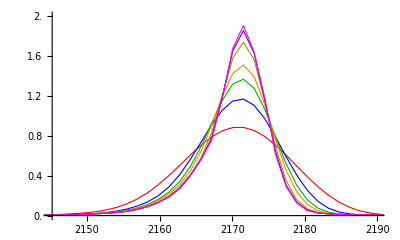

```mathematica
(*delay scaling*)
ListPlot[{ftir2ps40fs,ftir3ps40fs,ftir4ps40fs,ftir5ps40fs,ftir8ps40fs,ftir12ps40fs,ftir16ps40fs},PlotRange-> {{2145,2190},{0,2.0}},Joined-> True,PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]},{Darker[Green,0.3],Thickness[0.002]},{Orange,Thickness[0.002]},{Darker[Yellow,0.4],Thickness[0.002]},{Purple,Thickness[0.002]},{Magenta,Thickness[0.002]}},AspectRatio->0.6,AxesStyle-> Directive[Black,FontSize-> 18,Thickness-> 0.005],Ticks-> {Table[i,{i,2150,2190,10}],Table[i,{i,0,2.0,0.4}]},TicksStyle->Directive[Black,FontSize-> 14,Thickness-> 0.005]]
```

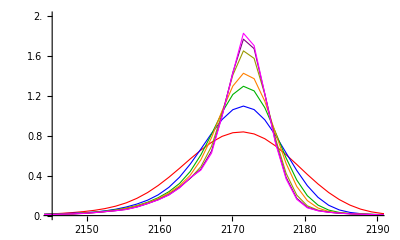

```mathematica
ListPlot[{ftir2ps80fs,ftir3ps80fs,ftir4ps80fs,ftir5ps80fs,ftir8ps80fs,ftir12ps80fs,ftir16ps80fs},PlotRange-> {{2145,2190},{0,2}},Joined-> True,PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]},{Darker[Green,0.3],Thickness[0.002]},{Orange,Thickness[0.002]},{Darker[Yellow,0.4],Thickness[0.002]},{Purple,Thickness[0.002]},{Magenta,Thickness[0.002]}},AspectRatio->0.6,AxesStyle-> Directive[Black,FontSize-> 18,Thickness-> 0.005],Ticks-> {Table[i,{i,2150,2190,10}],Table[i,{i,0,2,0.4}]},TicksStyle->Directive[Black,FontSize-> 14,Thickness-> 0.005]]
```

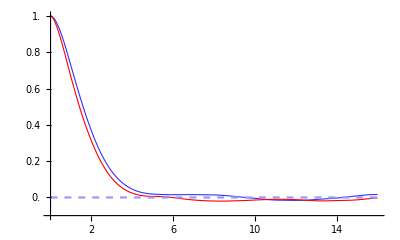

```mathematica
(*Jct*)
Show[ListPlot[{Jct40fs,Jct80fs},PlotRange-> {{0,16},{-0.1,1}},Joined-> True,PlotStyle->{{Lighter[Blue,0.2],Thickness[0.002]},{Red,Thickness[0.002]}},AspectRatio->0.6,AxesStyle-> Directive[Black,FontSize-> 18,Thickness-> 0.005],Ticks-> {Table[i,{i,2,16,2}],Table[i,{i,0,1,0.2}]},TicksStyle->Directive[Black,FontSize-> 14,Thickness-> 0.005],AxesOrigin->{0,-0.1}],Plot[0,{x,0,16},PlotStyle->{Dashed,Lighter[Blue,0.6]}]]
```

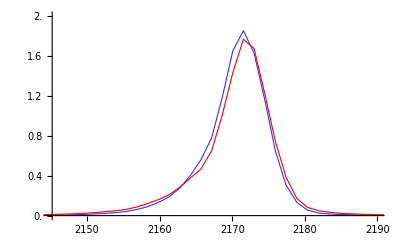

```mathematica
(*ftir: delay=12ps, d=40fs vs. d=80fs*)
ListPlot[{ftir12ps40fs,ftir12ps80fs},PlotRange-> {{2145,2190},{0,2}},Joined-> True,PlotStyle->{{Lighter[Blue,0.2],Thickness[0.002]},{Red,Thickness[0.002]}},AspectRatio->0.6,AxesStyle-> Directive[Black,FontSize-> 18,Thickness-> 0.005],Ticks-> {Table[i,{i,2150,2190,10}],Table[i,{i,0,2,0.4}]},TicksStyle->Directive[Black,FontSize-> 14,Thickness-> 0.005]]
```